```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data=ReadList["!./hw 100 1e-10 | awk '/^temp/{print $2, $3, $4}'",{Number,Number,Number}];
```

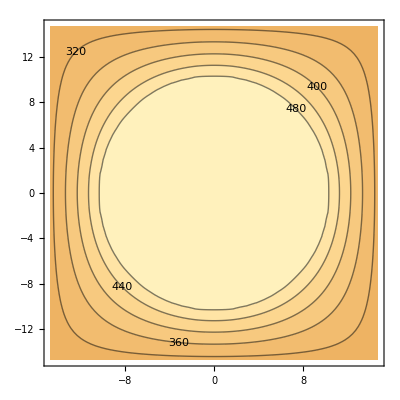

```mathematica
ListContourPlot[data,Contours->{300,320,360,400,440,480,500},ContourLabels->All]
```

```mathematica
datae=ReadList["!./hw 200 1e-1 | awk '/^grad/{print $2, $3, $4, $5}'",{Number,Number,Number,Number}];
```

```mathematica
ListVectorPlot[datae,RegionFunction->Function[{x,y},Abs[x]>0.5||Abs[y]>0.5],VectorScale->0.06]
```

$Aborted